#### Preamble

```mathematica
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],15*60]; (*Saves nb each 15 minutes*)
StartScheduledTask[saveTask]
```

ScheduledTaskObject[…]

```mathematica
SetDirectory[NotebookDirectory[]]
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Nano_CSM_SDistAll.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Nano_CSM_Biosensor.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Optical_functions/Au_JohnsnChristy.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/GradientDescend.wls"
```

/home/juanathan/gdrive/Collaborations/2022-06 INAOE/2-Reflectance_Measurments_NormalDist

```mathematica
fs = 9;
texStyle={FontFamily->"Latin Modern Math",FontSize->fs,Black};
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);

graphsOptsExp= {Mesh-> None,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 215, PlotStyle-> (Directive[Thick,#]&/@colors)};
graphsOptsTeo= {Mesh-> None,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 215, PlotStyle-> (Directive[#]&/@colors)};
```

#### Sample Characteristics

```mathematica
film = Import[#,"Data"]& @@ FileNames["1*fill.csv"];
TableForm[film[[2;;]],TableHeadings->{None,film[[1]]}]
radius = film[[2;;,2]];
muSigma = film[[2;;,{2,3}]];
cfrac = film[[2;;,4]]/100;
```

Nominal Au Thickness [+-0.2 nm] | Mean radius [nm] |  | Fill factor [100%] | 
3 | 5.78 | 1.89 | 20.3 | 0.6
5 | 7.3 | 2.3 | 22.1 | 0.1

```mathematica
nMat  = Import[#,"Data"] & @@ FileNames["3*Ind.csv"];
nMat = Drop[nMat,1];
nM = nMat[[1,2]]
```

1.33278

#### Experimental Spectra AuNI

```mathematica
(files = FileNames["*","Extinction*"])//TableForm
data = Import[#,"Data"]& /@ files;
wlen = Range[wlL = 450,wlR = 850,5.];
ang = {64.9,72.9} *Pi/180.;
nNP=JohnsonChristyAuRefSize[#1,#2]&;
pl = MapThread[Style["a = "<>ToString[#1]<>" nm, Θ = "<> ToString[#2],texStyle]&,{radius,cfrac}];
labels = Outer[#1<>" - θ_i = "<>#2<>"°"&,{"s-pol","p-pol"},ToString/@(ang*180/Pi)];
```

Extinction AuNI/Extinction AuNI nominal thickness d3nm_5nm 64_9deg.xlsx
Extinction AuNI/Extinction AuNI nominal thickness d3nm_5nm 72_9deg.xlsx

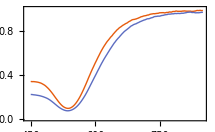
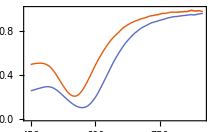
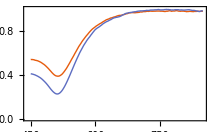
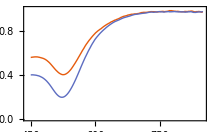

```mathematica
spectra = Map[Drop[#,4]&, data,{2}] (*Delete Headers*) ;
spectra = Map[Select[#,Function[list,wlL<=list[[1]]<= wlR]]&,spectra,{2}](*Choosing in the Visible*);
spectra = Map[Table[#[[{1,i}]]*{1,.01},{i,2,Length[#]}]&,spectra,{3}];
spectra = Transpose[spectra,{2,1,4,3,5}](*[[pol, ang, thickness, lda, Ext]]*);
spectra=spectra[[;;,;;,{1,2}]];

islandExt = Map[ListLinePlot[#,Evaluate[graphsOptsExp],PlotRange->{0,1}]&,spectra,{2}]
```

#### Poly

```mathematica
wlen = Range[wlL = 450,wlR = 850,5.];
ang = {64.9,72.9} *Pi/180.;
```

```mathematica
nominal = MapThread[ (
mu = First[#1];
sigma = Last[#1];
indAu = Transpose[Table[{nM,1.5},{i,wlen}]];
			norm2[CSMBioReflectionInt[ang,indAu,wlen,#2,{mu,sigma},"SizeDistribution"->"Normal"]])&,
{muSigma,cfrac}]; (*[[case, pol,ang,lda]]*)

nominal = Transpose[nominal,{3,1,2,4}](*[[pol,ang, case,lda]]*);
nominalplots = MapThread[ListLinePlot[#1,PlotLabel->#2,  DataRange->wlen[[{1,-1}]],Evaluate[graphsOptsTeo]]&,{nominal,labels},2];
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

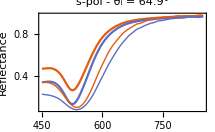
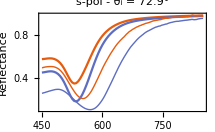
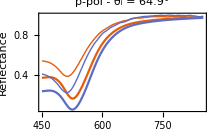
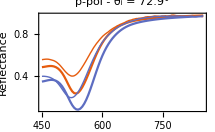

```mathematica
MapThread[Show[{#1,#2},PlotRange->All, FrameLabel-> (Style[#,texStyle]&/@{"Wavelength [nm]","Reflectance"})]&,{nominalplots,islandExt},2]
```

### FitModel (Gradient Descend) p Pol - Radius Only

{2,2,2,1569,2}

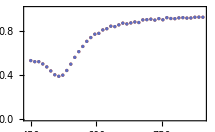
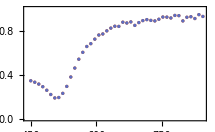
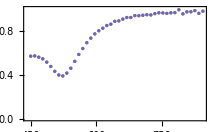
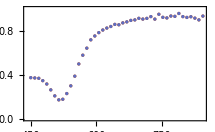

```mathematica
spectra//Dimensions (*[[pol, ang, thickness, lda, Ext]]*)
wl = spectra[[1,1,1,;;,1]];
take = Range[1,1569,36];
lambda = wl[[take]];

Map[ListPlot[{#[[take,2]],#[[take,2]]},DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsExp]]&,spectra[[2]],{2}]
```

```mathematica
indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
pol = 2; (*p Pol*)
bestRadius = ParallelTable[sigma = muSigma[[c,2]];
            f = norm2[CSMBioReflectionInt[ang[[t]],indAu,lambda,cfrac[[c]],{#,sigma},"SizeDistribution"->"Normal"][[pol]]]&;
            y = spectra[[pol,t,c,take,2]];
            error = Plus @@ (f[#] - y)^2/Length[lambda]&;
            result = AbsoluteTiming[
            Prepend[NGradientDescent[error,{7.},LearningRate -> "Barzilai-Borwein",Tolerance-> 1.*^-5],
            {{"s Pol","p Pol"}[[pol]], ang[[t]]*180./Pi,muSigma[[c,1]]}]];
            Print[{Date[], "\n", result}];
            result[[2]],
      {t, Length[ang]},
      {c,Length[muSigma]}];
      
exportData = Prepend[Flatten[Array[Flatten[bestRadius[[#1,#2]]] &,{2,2}],1],
{"Pol", "ang","mu","Best Radius","Error"}];
TableForm[exportData]
Export["2-BestRadiusFit-PPol-450nm-850nm.csv",exportData];
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{2023,3,17,10,30,25.701457},
,{238.516,{{p Pol,72.9,5.78},{3.40047},0.00391574}}}

{{2023,3,17,10,30,26.096148},
,{238.911,{{p Pol,64.9,5.78},{3.41567},0.00914577}}}

{{2023,3,17,10,33,46.188528},
,{200.092,{{p Pol,64.9,7.3},{4.20953},0.00666172}}}

{{2023,3,17,10,35,29.336887},
,{303.635,{{p Pol,72.9,7.3},{4.98122},3.59505×10^-11}}}

Pol | ang | mu | Best Radius | Error
p Pol | 64.9 | 5.78 | 3.41567 | 0.00914577
p Pol | 64.9 | 7.3 | 4.20953 | 0.00666172
p Pol | 72.9 | 5.78 | 3.40047 | 0.00391574
p Pol | 72.9 | 7.3 | 4.98122 | 3.59505×10^-11

```mathematica
pPol = Drop[Import["2-BestRadiusFit-PPol-450nm-850nm.csv","Data"],1];
pPol = Partition[#[[4]]&/@ pPol,2]
```

{{3.41567,4.20953},{3.40047,4.98122}}

```mathematica
indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
algo3 = Array[(a = pPol[[#1,#2]];
            sigma = muSigma[[#2,2]];
            f = norm2[CSMBioReflectionInt[ang[[#1]],indAu,lambda,cfrac[[#2]],{a,sigma},"SizeDistribution"->"Normal"][[2]]])&,
Dimensions[pPol]];(*pol, ang,case*)
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

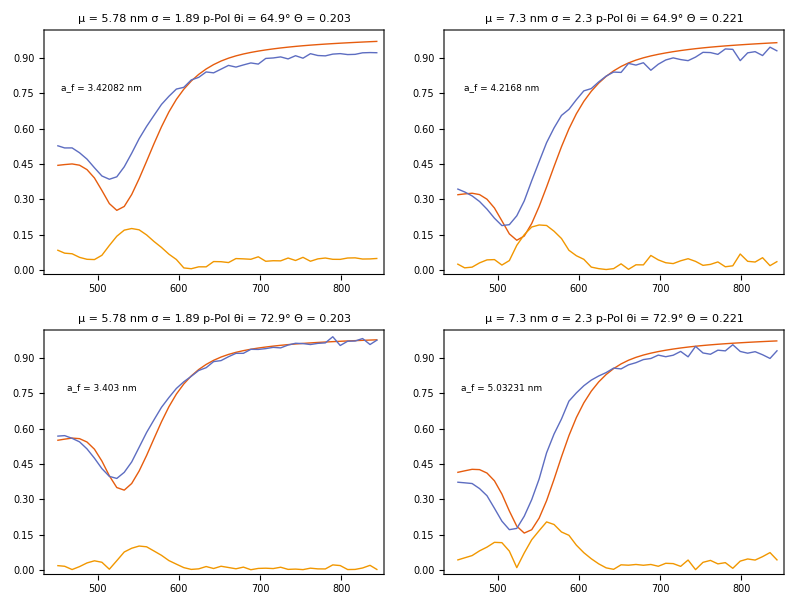

```mathematica
lb = Array[(sigma = "μ = "<>ToString@muSigma[[#2,1]]<>" nm σ = "<>ToString@muSigma[[#2,2]];
       pol = {"s-Pol","p-Pol"}[[2]];
       cf = "Θ = "<>ToString@cfrac[[#2]];
       deg = "θi = "<> ToString[ang[[#1]]/Degree]<>"°";
        sigma<>" "<>pol<>" "<>deg<>" "<>cf)&,
{2,2}];

Grid@MapThread[ListLinePlot[{#1,#2[[take,2]],Abs[#1-#2[[take,2]]]},DataRange->lambda[[{1,-1}]],PlotRange->1,PlotLabel->Style[#3,texStyle],Evaluate[graphsOptsExp],
Epilog->{Inset[Style["a_f = "<> ToString@#4<>" nm",texStyle],{505,.775}]}]&,{algo3,spectra[[2]],lb,pPol},2]
```

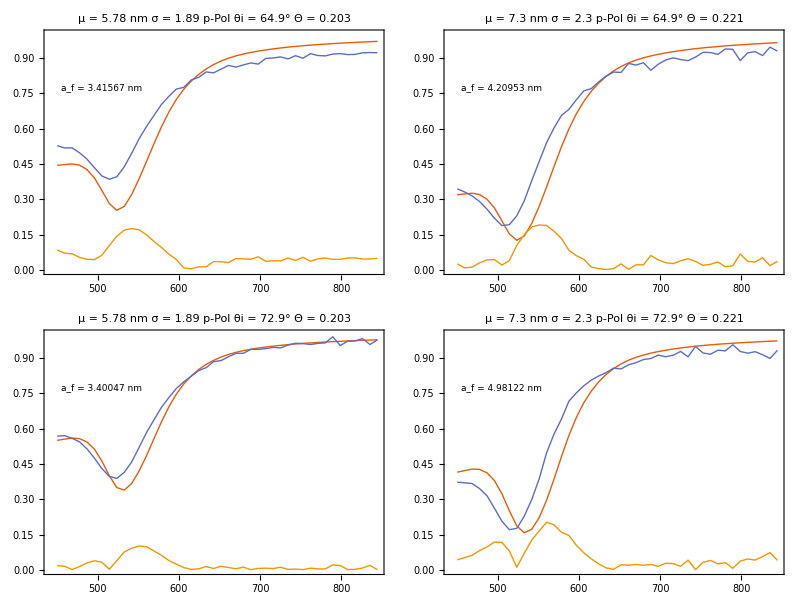

```mathematica
lb = Array[(sigma = "μ = "<>ToString@muSigma[[#2,1]]<>" nm σ = "<>ToString@muSigma[[#2,2]];
       pol = {"s-Pol","p-Pol"}[[2]];
       cf = "Θ = "<>ToString@cfrac[[#2]];
       deg = "θi = "<> ToString[ang[[#1]]/Degree]<>"°";
        sigma<>" "<>pol<>" "<>deg<>" "<>cf)&,
{2,2}];

Grid@MapThread[ListLinePlot[{#1,#2[[take,2]],Abs[#1-#2[[take,2]]]},DataRange->lambda[[{1,-1}]],PlotRange->1,PlotLabel->Style[#3,texStyle],Evaluate[graphsOptsExp],
Epilog->{Inset[Style["a_f = "<> ToString@#4<>" nm",texStyle],{505,.775}]}]&,{algo3,spectra[[2]],lb,pPol},2]
```

### FitModel (Gradient Descend) p Pol - Radius -- Θ

{2,2,2,3138,2}

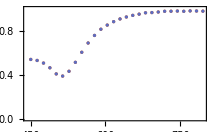
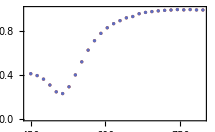
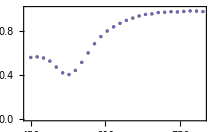
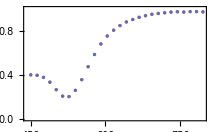

```mathematica
dir = "0-Fit-p-Pol";
name = "0-BestRadiusCFracFit-PPol-450nm-800nm.csv";

spectra//Dimensions (*[[pol, ang, thickness, lda, Ext]]*)
wl = spectra[[1,1,1,;;,1]];
take = Range[1,2750,100];
lambda = wl[[take]];

Map[ListPlot[{#[[take,2]],#[[take,2]]},DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsExp]]&,spectra[[2]],{2}]
```

```mathematica
indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
pol = 2; (*p Pol*)
bestRadius = ParallelTable[sigma = muSigma[[c,2]];
            f = norm2[CSMBioReflectionInt[ang[[t]],indAu,lambda,Abs[#2],{#1,sigma},"SizeDistribution"->"Normal"][[pol]]]&;
            y = spectra[[pol,t,c,take,2]];
            error = Plus @@ (f[#1,#2] - y)^2/Length[lambda]&;
            result = AbsoluteTiming[
            Prepend[NGradientDescent[error,{5.0, 0.18},LearningRate -> "Barzilai-Borwein",Tolerance-> 1.*^-8],
            {{"s Pol","p Pol"}[[pol]], ang[[t]]*180./Pi,muSigma[[c,1]]}]];
            Print[{Date[], "\n", result}];
            result[[2]],
      {t, Length[ang]},
      {c,Length[muSigma]}];
      
exportData = Prepend[Flatten[Array[Flatten[bestRadius[[#1,#2]]] &,{2,2}],1],
{"Pol", "ang","mu","Best Radius","Cfrac","Error"}];
TableForm[exportData]
Export[FileNameJoin[{dir,name}],exportData];
```

{{2023,5,2,14,53,39.201326},
,{2704.24,{{p Pol,64.9,5.78},{3.34602,0.138901},4.98174×10^-7}}}

{{2023,5,2,15,17,33.398753},
,{1433.93,{{p Pol,64.9,7.3},{4.07073,0.146939},5.60578×10^-7}}}

{{2023,5,2,15,52,58.43968},
,{6263.53,{{p Pol,72.9,5.78},{2.60397,3.86635},1.21705×10^-10}}}

{{2023,5,2,16,40,9.529265},
,{2831.09,{{p Pol,72.9,7.3},{4.15422,0.207049},5.51664×10^-7}}}

Pol | ang | mu | Best Radius | Cfrac | Error
p Pol | 64.9 | 5.78 | 3.34602 | 0.138901 | 4.98174×10^-7
p Pol | 64.9 | 7.3 | 4.07073 | 0.146939 | 5.60578×10^-7
p Pol | 72.9 | 5.78 | 2.60397 | 3.86635 | 1.21705×10^-10
p Pol | 72.9 | 7.3 | 4.15422 | 0.207049 | 5.51664×10^-7

```mathematica
pPol = Drop[Import[FileNameJoin[{dir,name}],"Data"],1];
radpPol = Partition[#[[4]]&/@ pPol,2]
cfracpPol = Partition[#[[5]]&/@ pPol,2]
```

{{3.34602,4.07073},{2.60397,4.15422}}

{{0.138901,0.146939},{3.86635,0.207049}}

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

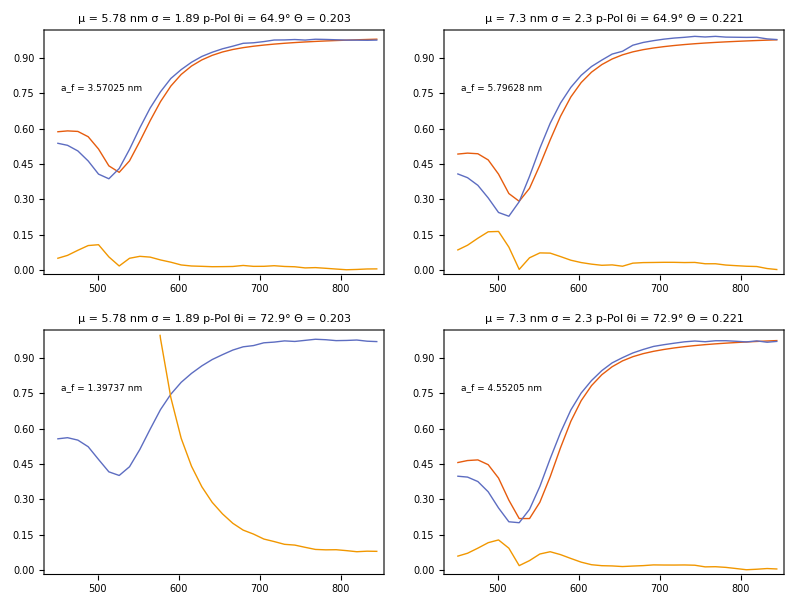

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

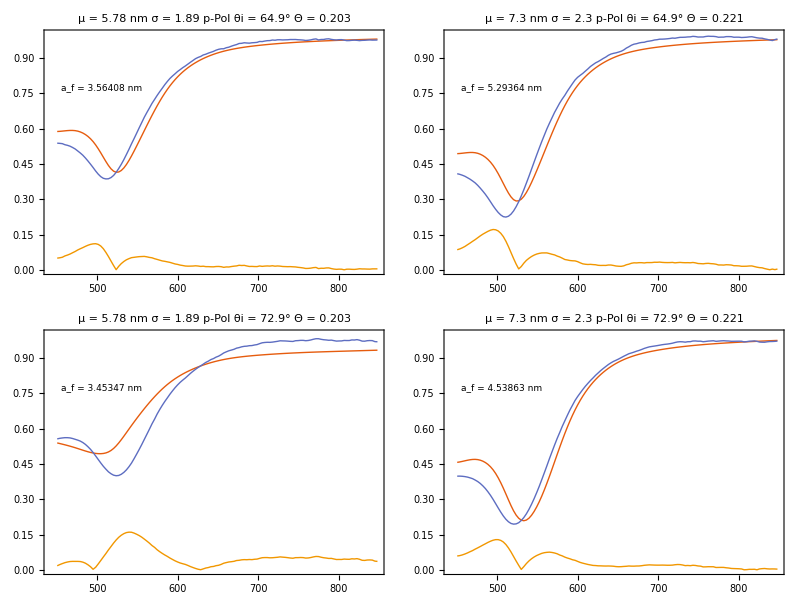

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

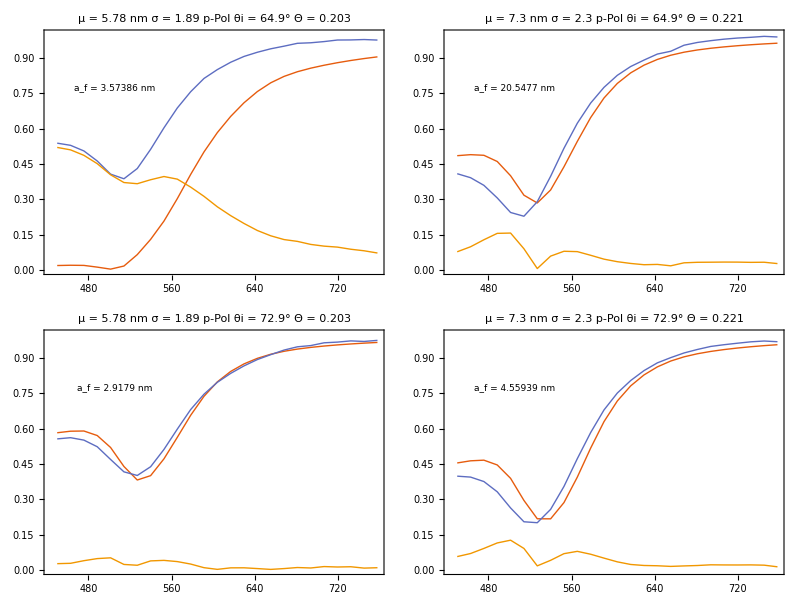

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

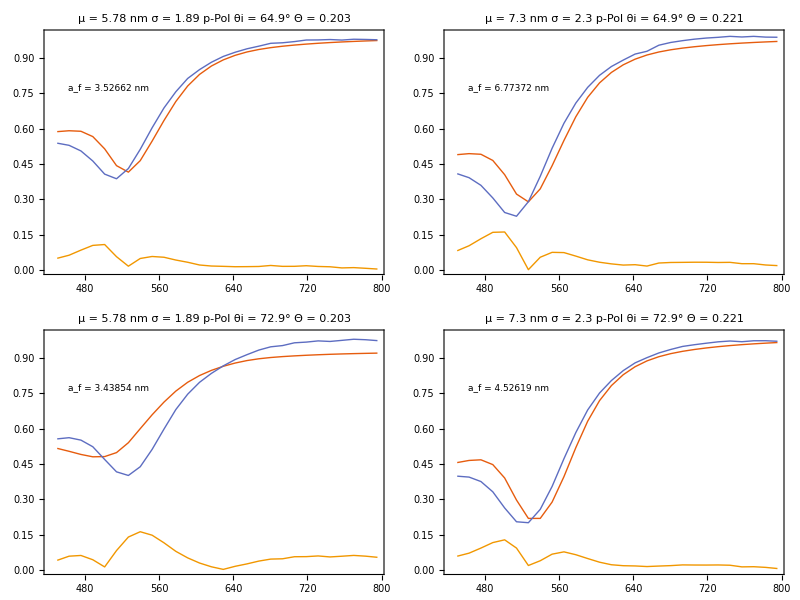

```mathematica
indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
algo3 = Array[(a = radpPol[[#1,#2]];
            cf = Abs@cfracpPol[[#1,#2]];
            sigma = muSigma[[#2,2]];
            f = norm2[CSMBioReflectionInt[ang[[#1]],indAu,lambda,cf,{a,sigma},"SizeDistribution"->"Normal"][[2]]])&,
Dimensions[radsPol]];(*pol, ang,case*)

lb = Array[(sigma = "μ = "<>ToString@muSigma[[#2,1]]<>" nm σ = "<>ToString@muSigma[[#2,2]];
       polL = {"s-Pol","p-Pol"}[[pol]];
       cf = "Θ = "<>ToString@cfrac[[#2]];
       deg = "θi = "<> ToString[ang[[#1]]/Degree]<>"°";
        sigma<>" "<>polL<>" "<>deg<>" "<>cf)&,
{2,2}];

Grid@MapThread[ListLinePlot[{#1,#2[[take,2]],Abs[#1-#2[[take,2]]]},DataRange->lambda[[{1,-1}]],PlotRange->1,PlotLabel->Style[#3,texStyle],Evaluate[graphsOptsExp],
Epilog->{Inset[Style["a_f = "<> ToString@#4<>" nm",texStyle],{505,.775}](*,
Inset[Style["b = "<> ToString@#5,texStyle],{505,.6}]*)}]&,{algo3,spectra[[pol]],lb,radsPol},2]
```

### FitModel (Gradient Descend) s Pol - Radius Only

{2,2,2,1569,2}

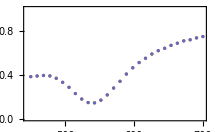
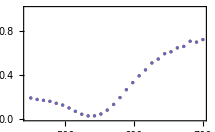
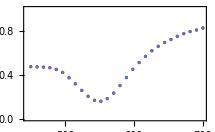
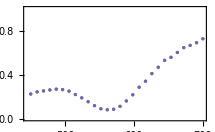

```mathematica
spectra//Dimensions (*[[pol, ang, thickness, lda, Ext]]*)
wl = spectra[[1,1,1,;;,1]];
take = Range[1,1000,36];
lambda = wl[[take]];

Map[ListPlot[{#[[take,2]],#[[take,2]]},DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsExp]]&,spectra[[1]],{2}]
```

```mathematica
indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
pol = 1; (*s Pol*)
bestRadius = ParallelTable[sigma = muSigma[[c,2]];
            f = norm2[CSMBioReflectionInt[ang[[t]],indAu,lambda,cfrac[[c]],{#,sigma},"SizeDistribution"->"Normal"][[pol]]]&;
            y = spectra[[pol,t,c,take,2]];
            error = Plus @@ (f[#1] - y)^2/Length[lambda]&;
            result = AbsoluteTiming[
            Prepend[NGradientDescent[error,{5.},LearningRate -> "Barzilai-Borwein",Tolerance-> 1.*^-8],
            {{"s Pol","p Pol"}[[pol]], ang[[t]]*180./Pi,muSigma[[c,1]]}]];
            Print[{Date[], "\n", result}];
            result[[2]],
      {t, Length[ang]},
      {c,Length[muSigma]}];
      
exportData = Prepend[Flatten[Array[Flatten[bestRadius[[#1,#2]]] &,{2,2}],1],
{"Pol", "ang","mu","Best Radius","Error"}];
TableForm[exportData]
Export["0-BestRadiusFit-SPol-450nm-673nm.csv",exportData];
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{2023,3,22,11,30,16.63939},
,{363.118,{{s Pol,64.9,5.78},{15.9786},3.4613×10^-11}}}

{{2023,3,22,11,31,30.609079},
,{437.088,{{s Pol,72.9,5.78},{3.32551},1.7027}}}

{{2023,3,22,11,33,53.541764},
,{216.902,{{s Pol,64.9,7.3},{4.0543},2.30488}}}

{{2023,3,22,11,35,13.18624},
,{222.577,{{s Pol,72.9,7.3},{4.0819},2.84612}}}

Pol | ang | mu | Best Radius | Error
s Pol | 64.9 | 5.78 | 15.9786 | 3.4613×10^-11
s Pol | 64.9 | 7.3 | 4.0543 | 2.30488
s Pol | 72.9 | 5.78 | 3.32551 | 1.7027
s Pol | 72.9 | 7.3 | 4.0819 | 2.84612

```mathematica
sPol = Drop[Import["0-BestRadiusFit-SPol-450nm-673nm.csv","Data"],1];
radsPol = Partition[#[[4]]&/@ sPol,2]
```

{{-7.83857,4.02621},{Indeterminate,4.06118}}

```mathematica
indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
algo3 = Array[(a = radsPol[[#1,#2]];
            sigma = muSigma[[#2,2]];
            f = norm2[CSMBioReflectionInt[ang[[#1]],indAu,lambda,cfrac[[#2]],{a,sigma},"SizeDistribution"->"Normal"][[1]]])&,
Dimensions[radsPol]];(*pol, ang,case*)

lb = Array[(sigma = "μ = "<>ToString@muSigma[[#2,1]]<>" nm σ = "<>ToString@muSigma[[#2,2]];
       pol = {"s-Pol","p-Pol"}[[1]];
       cf = "Θ = "<>ToString@cfrac[[#2]];
       deg = "θi = "<> ToString[ang[[#1]]/Degree]<>"°";
        sigma<>" "<>pol<>" "<>deg<>" "<>cf)&,
{2,2}];

Grid@MapThread[ListLinePlot[{#1,#2[[take,2]],Abs[#1-#2[[take,2]]]},DataRange->lambda[[{1,-1}]],PlotRange->1,PlotLabel->Style[#3,texStyle],Evaluate[graphsOptsExp],
Epilog->{Inset[Style["a_f = "<> ToString@#4<>" nm",texStyle],{505,.775}](*,
Inset[Style["b = "<> ToString@#5,texStyle],{505,.6}]*)}]&,{algo3,spectra[[1]],lb,radsPol},2]
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Table::iterb: Iterator {a,If[-9.45+Indeterminate<0,0,lim$1638956⟦1⟧],9.45+Indeterminate,1/40 Abs[9.45+Indeterminate-If[Plus[«2»]<0,0,lim$1638956⟦1⟧]]} does not have appropriate bounds.

Range::range: Range specification in Range[Ceiling[2.+1.0599 Indeterminate^0.333333+0.0186041 Indeterminate]] does not have appropriate bounds.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of 2 (-1005+Range[Ceiling[2.+1.0599 Indeterminate^0.333333+0.0186041 Indeterminate]]).

Range::range: Range specification in Range[(1+2. Ceiling[2.+1.0599 Power[«2»]+0.0186041 Indeterminate])/(Ceiling[2.+1.0599 Indeterminate^0.333333+0.0186041 Indeterminate] (1+Ceiling[2.+1.0599 Power[«2»]+0.0186041 Indeterminate]))] does not have appropriate bounds.

Range::range: Range specification in Range[1+2. Ceiling[2.+1.0599 Indeterminate^0.333333+0.0186041 Indeterminate]] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {(0.0646169 PDF[NormalDistribution[Indeterminate,1.89],Indeterminate])/Indeterminate^2,(0.0136394 ⅇ^(-0.139974 (Times[«2»]+If[«3»])^2))/Indeterminate^2,(5.08292×10^-8)/Indeterminate^2,(0.0136394 ⅇ^(-0.139974 (Times[«2»]+Times[«2»])^2))/Indeterminate^2} {{{0.5 (Range[Plus[«2»]]+Plus[«2»] Power[«2»]+Plus[«2»] Power[«2»])}},{{Range[Power[«2»] Power[«2»] Plus[«2»]]+(Hold[«1»] «1»)/Plus[«2»]+(Hold[Plus[«2»]] (Times[«1»]+«1»))/Plus[«2»]}},{{Range[Power[«2»] Power[«2»] Plus[«2»]]+(Hold[Plus[«2»]] (Times[«5»]+Times[«4»]))/Plus[«2»]+(Hold[Set[«2»]] (Times[«5»]+Times[«5»]))/Plus[«2»]}}} cannot be combined.

Transpose::nmtx: The first two levels of {{{{((5.19218×10^-14+7.0945×10^-8 ⅈ) PDF[NormalDistribution[Indeterminate,1.89],Indeterminate])/Indeterminate^2}},{{((5.19218×10^-14+7.09465×10^-8 ⅈ) PDF[NormalDistribution[Indeterminate,1.89],Indeterminate])/Indeterminate^2}},{{((6.82419×10^-14+9.32467×10^-8 ⅈ) PDF[NormalDistribution[Indeterminate,1.89],Indeterminate])/Indeterminate^2}}},{{{0.5 (Range[«1»]+Times[«2»]+Times[«2»])}},{{Range[Times[«3»]]+Hold[«1»] Plus[«2»] Power[«2»]+Hold[«1»] Plus[«2»] Power[«2»]}},{{Range[Times[«3»]]+Hold[«1»] Plus[«2»] Power[«2»]+Hold[«1»] Plus[«2»] Power[«2»]}}} {«1»}} cannot be transposed.

Table::iterb: Iterator {a,Table[a,{a,If[-9.45+Indeterminate<0,0,lim$1638956⟦1⟧],9.45+Indeterminate,1/40 Abs[9.45+Indeterminate-If[«3»]]}]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Table[a,{a,If[-9.45+Indeterminate<0,0,lim$1638956⟦1⟧],9.45+Indeterminate,1/40 Abs[9.45+Indeterminate-If[«3»]]}],{{((5.19218×10^-14+7.0945×10^-8 ⅈ) PDF[NormalDistribution[Indeterminate,1.89],Indeterminate])/Indeterminate^2},{{0.5 (Range[Plus[«2»]]+Plus[«2»] Power[«2»]+Plus[«2»] Power[«2»])}}}} cannot be transposed.

Interpolation::innd: First argument in Transpose[{Table[a,{a,If[-9.45+Indeterminate<0,0,lim$1638956⟦1⟧],9.45+Indeterminate,1/40 Abs[9.45+Indeterminate+Times[«2»]]}],{{((5.19218×10^-14+7.0945×10^-8 ⅈ) PDF[NormalDistribution[Indeterminate,1.89],Indeterminate])/Indeterminate^2},{{0.5 (Range[«1»]+Times[«2»]+Times[«2»])}}}}] does not contain a list of data and coordinates.

NIntegrate::nlim: a = 0.945+If[-9.45+Indeterminate<0.,0.,lim$1638956⟦1⟧] is not a valid limit of integration.

Transpose::nmtx: The first two levels of {Table[a,{a,If[-9.45+Indeterminate<0,0,lim$1638956⟦1⟧],9.45+Indeterminate,1/40 Abs[9.45+Indeterminate-If[«3»]]}],{{((5.19218×10^-14+7.0945×10^-8 ⅈ) PDF[NormalDistribution[Indeterminate,1.89],Indeterminate])/Indeterminate^2},{{0.5 (Range[Plus[«2»]]+Plus[«2»] Power[«2»]+Plus[«2»] Power[«2»])}}}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Interpolation::innd: First argument in Transpose[{Table[a,{a,If[-9.45+Indeterminate<0,0,lim$1638956⟦1⟧],9.45+Indeterminate,1/40 Abs[9.45+Indeterminate+Times[«2»]]}],{{((5.19218×10^-14+7.0945×10^-8 ⅈ) PDF[NormalDistribution[Indeterminate,1.89],Indeterminate])/Indeterminate^2},{{0.5 (Range[«1»]+Times[«2»]+Times[«2»])}}}}] does not contain a list of data and coordinates.

NIntegrate::nlim: a = 0.945+If[-9.45+Indeterminate<0.,0.,lim$1638956⟦1⟧] is not a valid limit of integration.

Interpolation::innd: First argument in Transpose[{Table[a,{a,If[-9.45+Indeterminate<0,0,lim$1638956⟦1⟧],9.45+Indeterminate,1/40 Abs[9.45+Indeterminate+Times[«2»]]}],{{((5.19218×10^-14+7.0945×10^-8 ⅈ) PDF[NormalDistribution[Indeterminate,1.89],Indeterminate])/Indeterminate^2},{{0.5 (Range[«1»]+Times[«2»]+Times[«2»])}}}}] does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

NIntegrate::nlim: a = 0.945+If[-9.45+Indeterminate<0.,0.,lim$1638956⟦1⟧] is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

Part::partw: Part 2 of Transpose[{{{{((5.19218×10^-14+7.0945×10^-8 ⅈ) PDF[NormalDistribution[«2»],Indeterminate])/Indeterminate^2}},{{((5.19218×10^-14+7.09465×10^-8 ⅈ) PDF[NormalDistribution[«2»],Indeterminate])/Indeterminate^2}},{{((6.82419×10^-14+9.32467×10^-8 ⅈ) PDF[NormalDistribution[«2»],Indeterminate])/Indeterminate^2}}},{{{0.5 Plus[«3»]}},{{Range[«1»]+Times[«3»]+Times[«3»]}},{{Range[«1»]+Times[«3»]+Times[«3»]}}} {(0.0646169 PDF[NormalDistribution[Indeterminate,1.89],Indeterminate])/Indeterminate^2,(«21» ⅇ^(«1»))/(I…te)^2,(«22»)/…^2,(0.0136394 ⅇ^(«1»))/Indeterminate^2}}] does not exist.

Part::partd: Part specification {Table[Exp[{{1.22542×10^-18+0.0073753 ⅈ}} 2 ⅈ a],{a,Table[a,{a,If[Less[«2»],0,Part[«2»]],9.45+Indeterminate,1/40 Abs[«1»]}]}],Table[Exp[{{-1.22542×10^-18+0.0073753 ⅈ}} 2 ⅈ a],{a,Table[a,{a,If[Less[«2»],0,Part[«2»]],9.45+Indeterminate,1/40 Abs[«1»]}]}]}⟦1,1;;All,1,1⟧ is longer than depth of object.

Part::partw: Part 2 of Transpose[{{{{((5.19218×10^-14+7.0945×10^-8 ⅈ) PDF[NormalDistribution[«2»],Indeterminate])/Indeterminate^2}},{{((5.19218×10^-14+7.09465×10^-8 ⅈ) PDF[NormalDistribution[«2»],Indeterminate])/Indeterminate^2}},{{((6.82419×10^-14+9.32467×10^-8 ⅈ) PDF[NormalDistribution[«2»],Indeterminate])/Indeterminate^2}}},{{{0.5 Plus[«3»]}},{{Range[«1»]+Times[«3»]+Times[«3»]}},{{Range[«1»]+Times[«3»]+Times[«3»]}}} {(0.0646169 PDF[NormalDistribution[Indeterminate,1.89],Indeterminate])/Indeterminate^2,(«21» ⅇ^(«1»))/(I…te)^2,(«22»)/…^2,(0.0136394 ⅇ^(«1»))/Indeterminate^2}}] does not exist.

Interpolation::inhr: Requested order is too high; order has been reduced to {1}.

Part::partd: Part specification {Table[Exp[{{(-0.0147506+2.45085×10^-18 ⅈ) a}}],{a,Table[a,{a,If[Less[«2»],0.,Part[«2»]],9.45+Indeterminate,0.025 Abs[«1»]}]}],Table[Exp[{{(-0.0147506-2.45085×10^-18 ⅈ) a}}],{a,Table[a,{a,If[Less[«2»],0.,Part[«2»]],9.45+Indeterminate,0.025 Abs[«1»]}]}]}⟦1,1;;All,1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {{{0.5 (Range[Plus[«2»]]+Plus[«2»] Power[«2»]+Plus[«2»] Power[«2»])}},{{Range[Power[«2»] Power[«2»] Plus[«2»]]+(Hold[Set[«2»]] (Times[«5»]+Times[«4»]))/Plus[«2»]+(Hold[Plus[«2»]] (Times[«5»]+Times[«5»]))/Plus[«2»]}},{{Range[Power[«2»] Power[«2»] Plus[«2»]]+(Hold[Plus[«2»]] (Times[«5»]+Times[«4»]))/Plus[«2»]+(Hold[Set[«2»]] (Times[«5»]+Times[«5»]))/Plus[«2»]}}} {(0.0646169 PDF[NormalDistribution[Indeterminate,1.89],Indeterminate])/Indeterminate^2,(0.0136394 («18»)^(-«20» «1»))/Indeterminate^2,(5.08292×10^-8)/(In…ate)^2,(0.0136394 2.71828^(-0.139974 («1»)^2))/Indeterminate^2} cannot be combined.

Part::partw: Part 2 of Transpose[{{{{((5.19218×10^-14+7.0945×10^-8 ⅈ) PDF[NormalDistribution[«2»],Indeterminate])/Indeterminate^2}},{{((5.19218×10^-14+7.09465×10^-8 ⅈ) PDF[NormalDistribution[«2»],Indeterminate])/Indeterminate^2}},{{((6.82419×10^-14+9.32467×10^-8 ⅈ) PDF[NormalDistribution[«2»],Indeterminate])/Indeterminate^2}}},{{{0.5 Plus[«3»]}},{{Range[«1»]+Times[«3»]+Times[«3»]}},{{Range[«1»]+Times[«3»]+Times[«3»]}}} {(0.0646169 PDF[NormalDistribution[Indeterminate,1.89],Indeterminate])/Indeterminate^2,(«21» («18»)^(«1»))/(I…e)^2,(«22»)/(«15»)^2,(0.0136394 («18»)^(«1»))/Indeterminate^2}}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::inhr: Requested order is too high; order has been reduced to {1}.

Thread::tdlen: Objects of unequal length in {{{0.5 (Range[Plus[«2»]]+Plus[«2»] Power[«2»]+Plus[«2»] Power[«2»])}},{{Range[Power[«2»] Power[«2»] Plus[«2»]]+(Hold[Set[«2»]] (Times[«5»]+Times[«4»]))/Plus[«2»]+(Hold[Plus[«2»]] (Times[«5»]+Times[«5»]))/Plus[«2»]}},{{Range[Power[«2»] Power[«2»] Plus[«2»]]+(Hold[Plus[«2»]] (Times[«5»]+Times[«4»]))/Plus[«2»]+(Hold[Set[«2»]] (Times[«5»]+Times[«5»]))/Plus[«2»]}}} {(0.0646169 PDF[NormalDistribution[Indeterminate,1.89],Indeterminate])/Indeterminate^2,(0.0136394 («18»)^(-«20» «1»))/Indeterminate^2,(5.08292×10^-8)/(In…ate)^2,(0.0136394 2.71828^(-0.139974 («1»)^2))/Indeterminate^2} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Interpolation::inhr: Requested order is too high; order has been reduced to {1}.

General::stop: Further output of Interpolation::inhr will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of 2 (-1005+Range[Ceiling[2.+1.0526 Indeterminate^0.333333+0.0182227 Indeterminate]]).

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$Aborted

Thread::tdlen: Objects of unequal length in {0.534559,0.537491,0.539635,0.534277,0.516592,0.48305,0.432555,0.379081,0.352493,0.371237,«27»}+{-0.381954,-0.387708,-0.392763,-0.38873,-0.367008,-0.330183,-0.284777,-0.227959,-0.177909,-0.145922,«15»} cannot be combined.

ListLinePlot::lpn: {{{450.121,0.534559},{456.315,0.537491},{462.509,0.539635},{468.704,0.534277},{474.898,0.516592},{481.092,0.48305},{487.286,0.432555},{493.48,0.379081},{499.674,0.352493},{505.869,0.371237},«27»},{{450.121,0.381954},{459.412,0.387708},{468.704,0.392763},«5»,{524.451,0.177909},{533.742,0.145922},«15»},{}} is not a list of numbers or pairs of numbers.

Thread::tdlen: Objects of unequal length in {0.418047,0.421231,0.423572,0.417415,0.397271,0.35929,0.302741,0.243813,0.215191,0.236557,«27»}+{-0.187851,-0.174384,-0.166101,-0.157004,-0.139261,-0.123098,-0.096743,-0.0660847,-0.0396358,-0.0246468,«15»} cannot be combined.

ListLinePlot::lpn: {{{450.121,0.418047},{456.315,0.421231},{462.509,0.423572},{468.704,0.417415},{474.898,0.397271},{481.092,0.35929},{487.286,0.302741},{493.48,0.243813},{499.674,0.215191},{505.869,0.236557},«27»},{{450.121,0.187851},{459.412,0.174384},{468.704,0.166101},{477.995,0.157004},«3»,{515.16,0.0660847},{524.451,0.0396358},{533.742,0.0246468},«15»},{}} is not a list of numbers or pairs of numbers.

Thread::tdlen: Objects of unequal length in {0.598415,0.602293,0.605604,0.602098,0.587025,0.555927,0.504586,0.440923,0.392383,0.388114,«27»}+{-0.472665,-0.471128,-0.468141,-0.463455,-0.447547,-0.420086,-0.372233,-0.317344,-0.256965,-0.202826,«15»} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

ListLinePlot::lpn: {{{450.121,0.598415},{456.315,0.602293},{462.509,0.605604},{468.704,0.602098},{474.898,0.587025},{481.092,0.555927},{487.286,0.504586},{493.48,0.440923},{499.674,0.392383},{505.869,0.388114},«27»},{{450.121,0.472665},{459.412,0.471128},{468.704,0.468141},{477.995,0.463455},«4»,{524.451,0.256965},{533.742,0.202826},«15»},{}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

ListLinePlot[{{0.534559,0.537491,0.539635,0.534277,0.516592,0.48305,0.432555,0.379081,0.352493,0.371237,0.422393,0.487075,0.555156,0.62213,0.683914,0.737439,0.781471,0.816753,0.844863,0.867414,0.885651,0.90043,0.912371,0.921952,0.929635,0.935897,0.941108,0.945544,0.949411,0.95284,0.955896,0.95863,0.961085,0.963295,0.965292,0.967105,0.968766},{0.381954,0.387708,0.392763,0.38873,0.367008,0.330183,0.284777,0.227959,0.177909,0.145922,0.143116,0.168007,0.215603,0.27808,0.339367,0.405696,0.462756,0.510445,0.549326,0.587987,0.618375,0.640152,0.66679,0.686404,0.707872},Abs[{-0.381954,-0.387708,-0.392763,-0.38873,-0.367008,-0.330183,-0.284777,-0.227959,-0.177909,-0.145922,-0.143116,-0.168007,-0.215603,-0.27808,-0.339367,-0.405696,-0.462756,-0.510445,-0.549326,-0.587987,-0.618375,-0.640152,-0.66679,-0.686404,-0.707872}+{0.534559,0.537491,0.539635,0.534277,0.516592,0.48305,0.432555,0.379081,0.352493,0.371237,0.422393,0.487075,0.555156,0.62213,0.683914,0.737439,0.781471,0.816753,0.844863,0.867414,0.885651,0.90043,0.912371,0.921952,0.929635,0.935897,0.941108,0.945544,0.949411,0.95284,0.955896,0.95863,0.961085,0.963295,0.965292,0.967105,0.968766}]},DataRange→{450.121,673.111},PlotRange→1,PlotLabel→μ = 5.78 nm σ = 1.89 s-Pol θi = 64.9° Θ = 0.203,{Mesh→None,BaseStyle→{FontFamily→Latin Modern Math,FontSize→9,GrayLevel[0]},Frame→True,FrameStyle→GrayLevel[0],ImageSize→215,PlotStyle→{Directive[Thickness[Large],RGBColor[0.9, 0.36, 0.054]],Directive[Thickness[Large],RGBColor[0.365248, 0.427802, 0.758297]],Directive[Thickness[Large],RGBColor[0.945109, 0.593901, 0.]],Directive[Thickness[Large],RGBColor[0.645957, 0.253192, 0.685109]],Directive[Thickness[Large],RGBColor[0.285821, 0.56, 0.450773]],Directive[Thickness[Large],RGBColor[0.7, 0.336, 0.]],Directive[Thickness[Large],RGBColor[0.491486, 0.345109, 0.8]],Directive[Thickness[Large],RGBColor[0.71788, 0.568653, 0.]],Directive[Thickness[Large],RGBColor[0.70743, 0.224, 0.542415]],Directive[Thickness[Large],RGBColor[0.287228, 0.490217, 0.664674]],Directive[Thickness[Large],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636]],Directive[Thickness[Large],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922]],Directive[Thickness[Large],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023]],Directive[Thickness[Large],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854]],Directive[Thickness[Large],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]]}},Epilog→{Inset[a_f = -7.83857 nm,{505,0.775}]}] | ListLinePlot[{{0.418047,0.421231,0.423572,0.417415,0.397271,0.35929,0.302741,0.243813,0.215191,0.236557,0.294721,0.370001,0.451395,0.533027,0.609239,0.675635,0.730427,0.774447,0.80962,0.83794,0.860885,0.879459,0.894404,0.906302,0.915749,0.923379,0.929683,0.935024,0.939672,0.943792,0.947463,0.950746,0.953689,0.956335,0.958721,0.960883,0.962863},{0.187851,0.174384,0.166101,0.157004,0.139261,0.123098,0.096743,0.0660847,0.0396358,0.0246468,0.0251664,0.0417391,0.0774048,0.128985,0.191323,0.26309,0.327487,0.3897,0.443534,0.506718,0.54231,0.591104,0.608512,0.644207,0.657241},Abs[{-0.187851,-0.174384,-0.166101,-0.157004,-0.139261,-0.123098,-0.096743,-0.0660847,-0.0396358,-0.0246468,-0.0251664,-0.0417391,-0.0774048,-0.128985,-0.191323,-0.26309,-0.327487,-0.3897,-0.443534,-0.506718,-0.54231,-0.591104,-0.608512,-0.644207,-0.657241}+{0.418047,0.421231,0.423572,0.417415,0.397271,0.35929,0.302741,0.243813,0.215191,0.236557,0.294721,0.370001,0.451395,0.533027,0.609239,0.675635,0.730427,0.774447,0.80962,0.83794,0.860885,0.879459,0.894404,0.906302,0.915749,0.923379,0.929683,0.935024,0.939672,0.943792,0.947463,0.950746,0.953689,0.956335,0.958721,0.960883,0.962863}]},DataRange→{450.121,673.111},PlotRange→1,PlotLabel→μ = 7.3 nm σ = 2.3 s-Pol θi = 64.9° Θ = 0.221,{Mesh→None,BaseStyle→{FontFamily→Latin Modern Math,FontSize→9,GrayLevel[0]},Frame→True,FrameStyle→GrayLevel[0],ImageSize→215,PlotStyle→{Directive[Thickness[Large],RGBColor[0.9, 0.36, 0.054]],Directive[Thickness[Large],RGBColor[0.365248, 0.427802, 0.758297]],Directive[Thickness[Large],RGBColor[0.945109, 0.593901, 0.]],Directive[Thickness[Large],RGBColor[0.645957, 0.253192, 0.685109]],Directive[Thickness[Large],RGBColor[0.285821, 0.56, 0.450773]],Directive[Thickness[Large],RGBColor[0.7, 0.336, 0.]],Directive[Thickness[Large],RGBColor[0.491486, 0.345109, 0.8]],Directive[Thickness[Large],RGBColor[0.71788, 0.568653, 0.]],Directive[Thickness[Large],RGBColor[0.70743, 0.224, 0.542415]],Directive[Thickness[Large],RGBColor[0.287228, 0.490217, 0.664674]],Directive[Thickness[Large],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636]],Directive[Thickness[Large],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922]],Directive[Thickness[Large],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023]],Directive[Thickness[Large],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854]],Directive[Thickness[Large],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]]}},Epilog→{Inset[a_f = 4.02621 nm,{505,0.775}]}]
ListLinePlot[{{0.598415,0.602293,0.605604,0.602098,0.587025,0.555927,0.504586,0.440923,0.392383,0.388114,0.425903,0.487159,0.557847,0.630318,0.697782,0.755506,0.801842,0.837926,0.865891,0.887781,0.905094,0.918832,0.929708,0.938254,0.944968,0.950339,0.954737,0.958431,0.961617,0.964418,0.966896,0.969095,0.971055,0.972806,0.974377,0.975794,0.977085},{0.472665,0.471128,0.468141,0.463455,0.447547,0.420086,0.372233,0.317344,0.256965,0.202826,0.166349,0.15739,0.181974,0.231881,0.300511,0.37386,0.448467,0.51069,0.5668,0.617656,0.657786,0.692966,0.720102,0.749021,0.773748},Abs[{-0.472665,-0.471128,-0.468141,-0.463455,-0.447547,-0.420086,-0.372233,-0.317344,-0.256965,-0.202826,-0.166349,-0.15739,-0.181974,-0.231881,-0.300511,-0.37386,-0.448467,-0.51069,-0.5668,-0.617656,-0.657786,-0.692966,-0.720102,-0.749021,-0.773748}+{0.598415,0.602293,0.605604,0.602098,0.587025,0.555927,0.504586,0.440923,0.392383,0.388114,0.425903,0.487159,0.557847,0.630318,0.697782,0.755506,0.801842,0.837926,0.865891,0.887781,0.905094,0.918832,0.929708,0.938254,0.944968,0.950339,0.954737,0.958431,0.961617,0.964418,0.966896,0.969095,0.971055,0.972806,0.974377,0.975794,0.977085}]},DataRange→{450.121,673.111},PlotRange→1,PlotLabel→μ = 5.78 nm σ = 1.89 s-Pol θi = 72.9° Θ = 0.203,{Mesh→None,BaseStyle→{FontFamily→Latin Modern Math,FontSize→9,GrayLevel[0]},Frame→True,FrameStyle→GrayLevel[0],ImageSize→215,PlotStyle→{Directive[Thickness[Large],RGBColor[0.9, 0.36, 0.054]],Directive[Thickness[Large],RGBColor[0.365248, 0.427802, 0.758297]],Directive[Thickness[Large],RGBColor[0.945109, 0.593901, 0.]],Directive[Thickness[Large],RGBColor[0.645957, 0.253192, 0.685109]],Directive[Thickness[Large],RGBColor[0.285821, 0.56, 0.450773]],Directive[Thickness[Large],RGBColor[0.7, 0.336, 0.]],Directive[Thickness[Large],RGBColor[0.491486, 0.345109, 0.8]],Directive[Thickness[Large],RGBColor[0.71788, 0.568653, 0.]],Directive[Thickness[Large],RGBColor[0.70743, 0.224, 0.542415]],Directive[Thickness[Large],RGBColor[0.287228, 0.490217, 0.664674]],Directive[Thickness[Large],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636]],Directive[Thickness[Large],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922]],Directive[Thickness[Large],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023]],Directive[Thickness[Large],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854]],Directive[Thickness[Large],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]]}},Epilog→{Inset[a_f = Indeterminate nm,{505,0.775}]}] | ListLinePlot[{{0.521651,0.526733,0.531257,0.528338,0.512787,0.479819,0.424964,0.356218,0.300773,0.288784,0.32129,0.382066,0.457257,0.538509,0.617396,0.687155,0.744534,0.789989,0.825627,0.853737,0.876092,0.893908,0.908065,0.919231,0.928033,0.935095,0.940887,0.945758,0.949959,0.953651,0.956915,0.95981,0.96239,0.964695,0.966761,0.968624,0.97032},{0.223902,0.243235,0.252126,0.260871,0.267947,0.264174,0.250198,0.219293,0.189148,0.153835,0.117845,0.0893505,0.0803361,0.0852222,0.111281,0.160518,0.21704,0.285107,0.340195,0.409733,0.467133,0.530195,0.557707,0.602186,0.646272},Abs[{-0.223902,-0.243235,-0.252126,-0.260871,-0.267947,-0.264174,-0.250198,-0.219293,-0.189148,-0.153835,-0.117845,-0.0893505,-0.0803361,-0.0852222,-0.111281,-0.160518,-0.21704,-0.285107,-0.340195,-0.409733,-0.467133,-0.530195,-0.557707,-0.602186,-0.646272}+{0.521651,0.526733,0.531257,0.528338,0.512787,0.479819,0.424964,0.356218,0.300773,0.288784,0.32129,0.382066,0.457257,0.538509,0.617396,0.687155,0.744534,0.789989,0.825627,0.853737,0.876092,0.893908,0.908065,0.919231,0.928033,0.935095,0.940887,0.945758,0.949959,0.953651,0.956915,0.95981,0.96239,0.964695,0.966761,0.968624,0.97032}]},DataRange→{450.121,673.111},PlotRange→1,PlotLabel→μ = 7.3 nm σ = 2.3 s-Pol θi = 72.9° Θ = 0.221,{Mesh→None,BaseStyle→{FontFamily→Latin Modern Math,FontSize→9,GrayLevel[0]},Frame→True,FrameStyle→GrayLevel[0],ImageSize→215,PlotStyle→{Directive[Thickness[Large],RGBColor[0.9, 0.36, 0.054]],Directive[Thickness[Large],RGBColor[0.365248, 0.427802, 0.758297]],Directive[Thickness[Large],RGBColor[0.945109, 0.593901, 0.]],Directive[Thickness[Large],RGBColor[0.645957, 0.253192, 0.685109]],Directive[Thickness[Large],RGBColor[0.285821, 0.56, 0.450773]],Directive[Thickness[Large],RGBColor[0.7, 0.336, 0.]],Directive[Thickness[Large],RGBColor[0.491486, 0.345109, 0.8]],Directive[Thickness[Large],RGBColor[0.71788, 0.568653, 0.]],Directive[Thickness[Large],RGBColor[0.70743, 0.224, 0.542415]],Directive[Thickness[Large],RGBColor[0.287228, 0.490217, 0.664674]],Directive[Thickness[Large],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636]],Directive[Thickness[Large],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922]],Directive[Thickness[Large],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023]],Directive[Thickness[Large],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854]],Directive[Thickness[Large],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]]}},Epilog→{Inset[a_f = 4.06118 nm,{505,0.775}]}]

### FitModel (Gradient Descend) s Pol - Radius Multi

{2,2,2,1569,2}

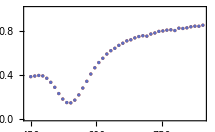
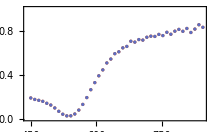
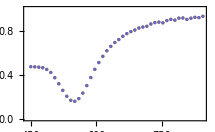
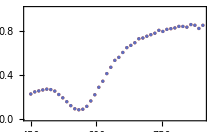

```mathematica
spectra//Dimensions (*[[pol, ang, thickness, lda, Ext]]*)
wl = spectra[[1,1,1,;;,1]];
take = Range[1,1569,36];
lambda = wl[[take]];

Map[ListPlot[{#[[take,2]],#[[take,2]]},DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsExp]]&,spectra[[1]],{2}]
```

```mathematica
indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
pol = 1; (*s Pol*)
bestRadius = ParallelTable[sigma = muSigma[[c,2]];
            f = norm2[CSMBioReflectionInt[ang[[t]],indAu,lambda,cfrac[[c]],{#,sigma},"SizeDistribution"->"Normal"][[pol]]]&;
            y = spectra[[pol,t,c,take,2]];
            error = Plus @@ (#2 * f[#1] - y)^2/Length[lambda]&;
            result = AbsoluteTiming[
            Prepend[NGradientDescent[error,{5.,.5},LearningRate -> "Barzilai-Borwein",Tolerance-> 1.*^-8],
            {{"s Pol","p Pol"}[[pol]], ang[[t]]*180./Pi,muSigma[[c,1]]}]];
            Print[{Date[], "\n", result}];
            result[[2]],
      {t, Length[ang]},
      {c,Length[muSigma]}];
      
exportData = Prepend[Flatten[Array[Flatten[bestRadius[[#1,#2]]] &,{2,2}],1],
{"Pol", "ang","mu","Best Radius","Offset","Error"}];
TableForm[exportData]
Export["0-BestRadiusOffFit-SPol-450nm-900nm.csv",exportData];
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{2023,3,23,2,25,49.032482},
,{2706.52,{{s Pol,64.9,5.78},{3.37755,0.73295},2.67916×10^-7}}}

{{2023,3,23,2,29,21.867975},
,{2919.35,{{s Pol,72.9,5.78},{3.37913,0.771481},2.93798×10^-7}}}

{{2023,3,23,2,51,24.129764},
,{1535.1,{{s Pol,64.9,7.3},{4.13686,0.662108},2.34569×10^-7}}}

{{2023,3,23,2,54,33.918176},
,{1512.05,{{s Pol,72.9,7.3},{4.14022,0.658537},2.55358×10^-7}}}

Pol | ang | mu | Best Radius | Offset | Error
s Pol | 64.9 | 5.78 | 3.37755 | 0.73295 | 2.67916×10^-7
s Pol | 64.9 | 7.3 | 4.13686 | 0.662108 | 2.34569×10^-7
s Pol | 72.9 | 5.78 | 3.37913 | 0.771481 | 2.93798×10^-7
s Pol | 72.9 | 7.3 | 4.14022 | 0.658537 | 2.55358×10^-7

```mathematica
sPol = Drop[Import["0-BestRadiusOffFit-SPol-450nm-900nm.csv","Data"],1];
radsPol = Partition[#[[4]]&/@ sPol,2]
ampsPol = Partition[#[[5]]&/@ sPol,2]
```

{{3.37755,4.13686},{3.37913,4.14022}}

{{0.73295,0.662108},{0.771481,0.658537}}

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

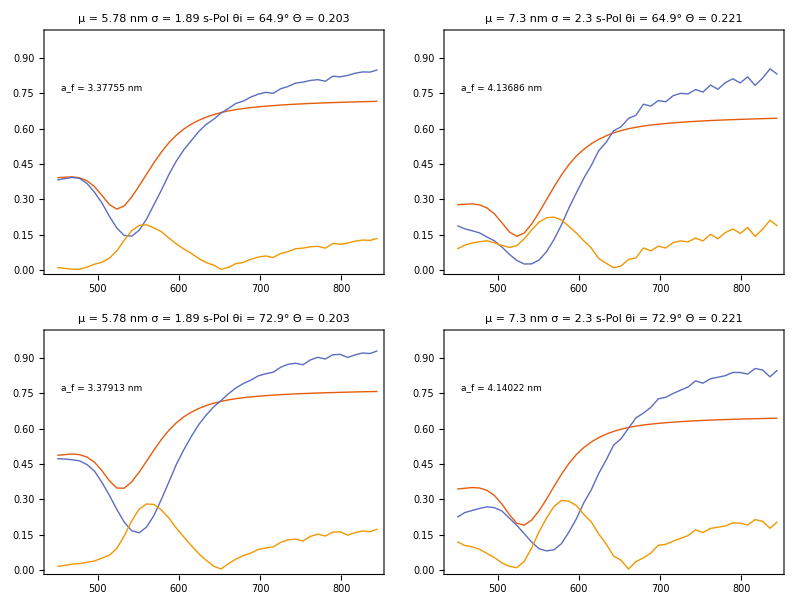

```mathematica
indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
algo3 = Array[(a = radsPol[[#1,#2]];
            b = ampsPol[[#1,#2]];
            sigma = muSigma[[#2,2]];
            f = b*norm2[CSMBioReflectionInt[ang[[#1]],indAu,lambda,cfrac[[#2]],{a,sigma},"SizeDistribution"->"Normal"][[pol]]])&,
Dimensions[radsPol]];(*pol, ang,case*)

lb = Array[(sigma = "μ = "<>ToString@muSigma[[#2,1]]<>" nm σ = "<>ToString@muSigma[[#2,2]];
       polL = {"s-Pol","p-Pol"}[[pol]];
       cf = "Θ = "<>ToString@cfrac[[#2]];
       deg = "θi = "<> ToString[ang[[#1]]/Degree]<>"°";
        sigma<>" "<>polL<>" "<>deg<>" "<>cf)&,
{2,2}];

Grid@MapThread[ListLinePlot[{#1,#2[[take,2]],Abs[#1-#2[[take,2]]]},DataRange->lambda[[{1,-1}]],PlotRange->1,PlotLabel->Style[#3,texStyle],Evaluate[graphsOptsExp],
Epilog->{Inset[Style["a_f = "<> ToString@#4<>" nm",texStyle],{505,.775}](*,
Inset[Style["b = "<> ToString@#5,texStyle],{505,.6}]*)}]&,{algo3,spectra[[pol]],lb,radsPol,ampsPol},2]
```

### FitModel (Gradient Descend) s Pol - Radius -- Θ

{2,2,2,3138,2}

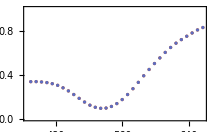
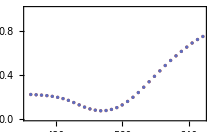
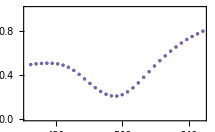
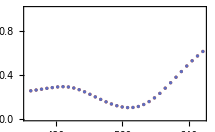

```mathematica
dir = "0-Fit-s-Pol";
name = "1-BestRadiusCFracFit-SPol-450nm-60nm.csv";
spectra//Dimensions (*[[pol, ang, thickness, lda, Ext]]*)
wl = spectra[[1,1,1,;;,1]];
take = Range[1,1620,50];
lambda = wl[[take]];

Map[ListPlot[{#[[take,2]],#[[take,2]]},DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsExp]]&,spectra[[1]],{2}]
```

```mathematica
indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
pol = 1; (*s Pol*)
bestRadius = ParallelTable[sigma = muSigma[[c,2]];
            f = norm2[CSMBioReflectionInt[ang[[t]],indAu,lambda,Abs[#2],{#1,sigma},"SizeDistribution"->"Normal"][[pol]]]&;
            y = spectra[[pol,t,c,take,2]];
            error = Plus @@ (f[#1,#2] - y)^2/Length[lambda]&;
            result = AbsoluteTiming[
            Prepend[NGradientDescent[error,{5.0, 0.18},LearningRate -> "Barzilai-Borwein",Tolerance-> 1.*^-8],
            {{"s Pol","p Pol"}[[pol]], ang[[t]]*180./Pi,muSigma[[c,1]]}]];
            Print[{Date[], "\n", result}];
            result[[2]],
      {t, Length[ang]},
      {c,Length[muSigma]}];
      
exportData = Prepend[Flatten[Array[Flatten[bestRadius[[#1,#2]]] &,{2,2}],1],
{"Pol", "ang","mu","Best Radius","Cfrac","Error"}];
TableForm[exportData]
Export[FileNameJoin[{dir,name}],exportData];
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{2023,5,15,17,51,55.078707},
,{1810.02,{{s Pol,64.9,5.78},{3.41467,0.440446},1.29383×10^-7}}}

{{2023,5,15,17,52,52.93686},
,{1867.88,{{s Pol,72.9,5.78},{3.34352,0.360287},5.19649×10^-7}}}

{{2023,5,15,18,44,20.055224},
,{3144.98,{{s Pol,64.9,7.3},{2.74106,0.647949},2.59636×10^-9}}}

{{2023,5,15,18,44,43.718979},
,{3110.78,{{s Pol,72.9,7.3},{4.31888,0.47367},1.62998×10^-7}}}

Pol | ang | mu | Best Radius | Cfrac | Error
s Pol | 64.9 | 5.78 | 3.41467 | 0.440446 | 1.29383×10^-7
s Pol | 64.9 | 7.3 | 2.74106 | 0.647949 | 2.59636×10^-9
s Pol | 72.9 | 5.78 | 3.34352 | 0.360287 | 5.19649×10^-7
s Pol | 72.9 | 7.3 | 4.31888 | 0.47367 | 1.62998×10^-7

```mathematica
sPol = Drop[Import[FileNameJoin[{dir,name}],"Data"],1];
radsPol = Partition[#[[4]]&/@ sPol,2]
cfracsPol = Partition[#[[5]]&/@ sPol,2]
```

{{3.41467,2.74106},{3.34352,4.31888}}

{{0.440446,0.647949},{0.360287,0.47367}}

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

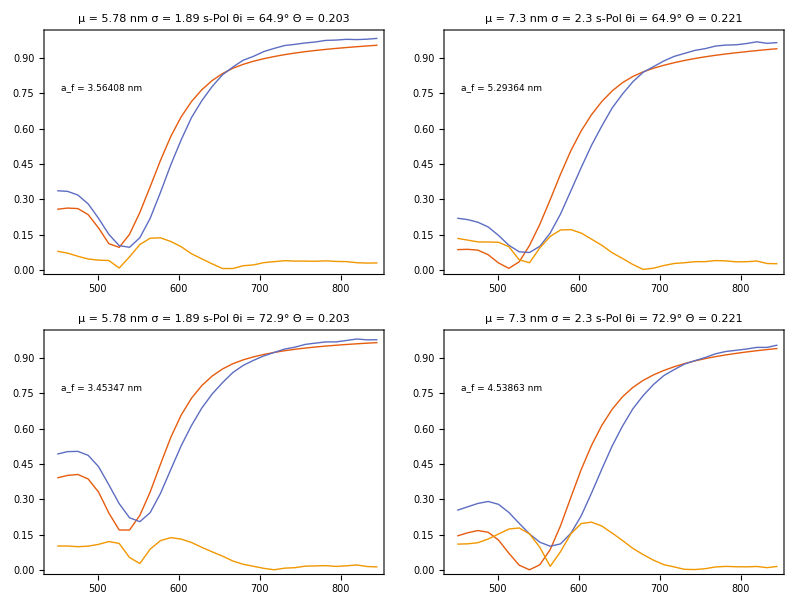

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

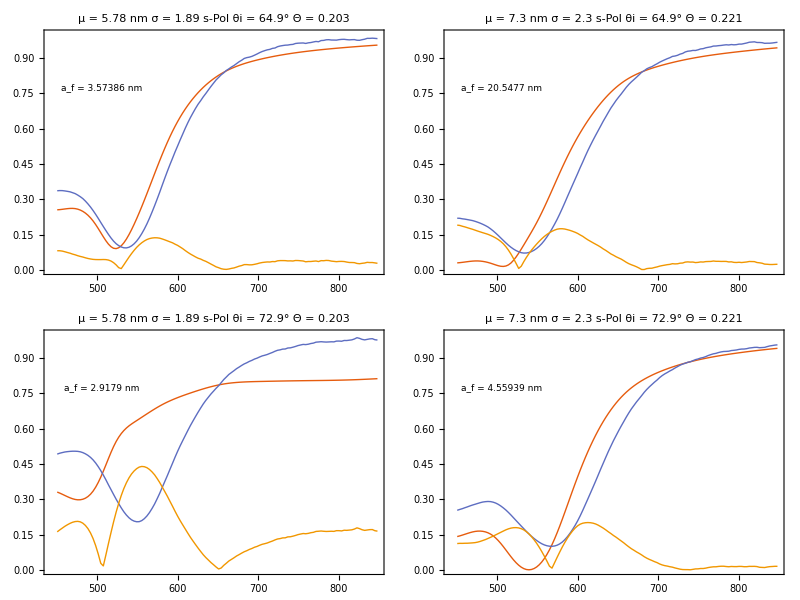

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

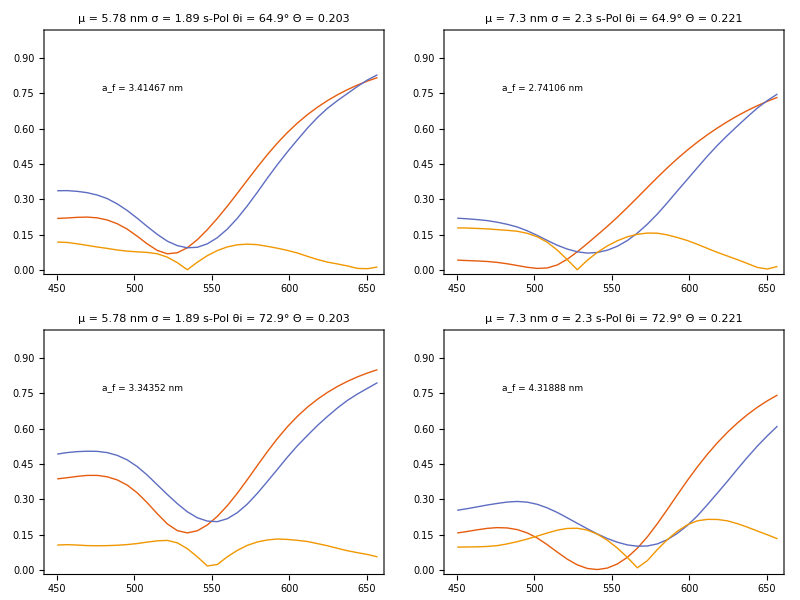

```mathematica
indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
algo3 = Array[(a = radsPol[[#1,#2]];
            cf = Abs@cfracsPol[[#1,#2]];
            sigma = muSigma[[#2,2]];
            f = norm2[CSMBioReflectionInt[ang[[#1]],indAu,lambda,cf,{a,sigma},"SizeDistribution"->"Normal"][[pol]]])&,
Dimensions[radsPol]];(*pol, ang,case*)

lb = Array[(sigma = "μ = "<>ToString@muSigma[[#2,1]]<>" nm σ = "<>ToString@muSigma[[#2,2]];
       polL = {"s-Pol","p-Pol"}[[pol]];
       cf = "Θ = "<>ToString@cfrac[[#2]];
       deg = "θi = "<> ToString[ang[[#1]]/Degree]<>"°";
        sigma<>" "<>polL<>" "<>deg<>" "<>cf)&,
{2,2}];

Grid@MapThread[ListLinePlot[{#1,#2[[take,2]],Abs[#1-#2[[take,2]]]},DataRange->lambda[[{1,-1}]],PlotRange->1,PlotLabel->Style[#3,texStyle],Evaluate[graphsOptsExp],
Epilog->{Inset[Style["a_f = "<> ToString@#4<>" nm",texStyle],{505,.775}](*,
Inset[Style["b = "<> ToString@#5,texStyle],{505,.6}]*)}]&,{algo3,spectra[[pol]],lb,radsPol},2]
```

### FitModel (Gradient Descend) s Pol - Radius - offset - Θ

{2,2,2,3138,2}

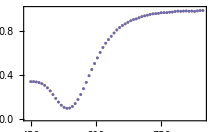
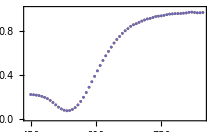
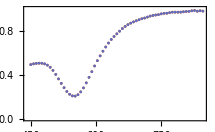
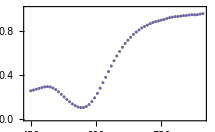

```mathematica
spectra//Dimensions (*[[pol, ang, thickness, lda, Ext]]*)
wl = spectra[[1,1,1,;;,1]];
take = Range[1,3150,50];
lambda = wl[[take]];

Map[ListPlot[{#[[take,2]],#[[take,2]]},DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsExp]]&,spectra[[1]],{2}]
```

```mathematica
indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
pol = 1; (*p Pol*)
bestRadius = ParallelTable[sigma = muSigma[[c,2]];
            f = norm2[CSMBioReflectionInt[ang[[t]],indAu,lambda,Abs[#2],{#1,sigma},"SizeDistribution"->"Normal"][[pol]]]&;
            y = spectra[[pol,t,c,take,2]];
            error = Plus @@ (#3*f[#1,#2] - y)^2/Length[lambda]&;
            result = AbsoluteTiming[
            Prepend[NGradientDescent[error,{5.0, 0.18, 0.5},LearningRate -> "Barzilai-Borwein",Tolerance-> 1.*^-8],
            {{"s Pol","p Pol"}[[pol]], ang[[t]]*180./Pi,muSigma[[c,1]]}]];
            Print[{Date[], "\n", result}];
            result[[2]],
      {t, Length[ang]},
      {c,Length[muSigma]}];
      
exportData = Prepend[Flatten[Array[Flatten[bestRadius[[#1,#2]]] &,{2,2}],1],
{"Pol", "ang","mu","Best Radius","Cfrac","Offset","Error"}];
TableForm[exportData]
Export["0-BestRadiusCFracFit-SPol-450nm-900nm.csv",exportData];
```

$Aborted

Pol | ang | mu | Best Radius | Cfrac | Offset | Error
p Pol | 64.9 | 5.78 | 3.36366 | 0.13879 | 8.85535×10^-7 | 
p Pol | 64.9 | 7.3 | 4.09755 | 0.145596 | 1.00663×10^-6 | 
p Pol | 72.9 | 5.78 | 1.69209 | -3.83682 | 1.04237×10^-10 | 
p Pol | 72.9 | 7.3 | 4.17573 | 0.206782 | 9.86411×10^-7 |

```mathematica
sPol = Drop[Import["0-BestRadiusCFracFit-SPol-450nm-900nm.csv","Data"],1];
radsPol = Partition[#[[4]]&/@ sPol,2]
cfracsPol = Partition[#[[5]]&/@ sPol,2]
offsPol = Partition[#[[6]]&/@ sPol,2]
```

{{0.91449,4.02615},{3.30706,4.05683}}

{{1.04217,0.472954},{0.63042,0.461598}}

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

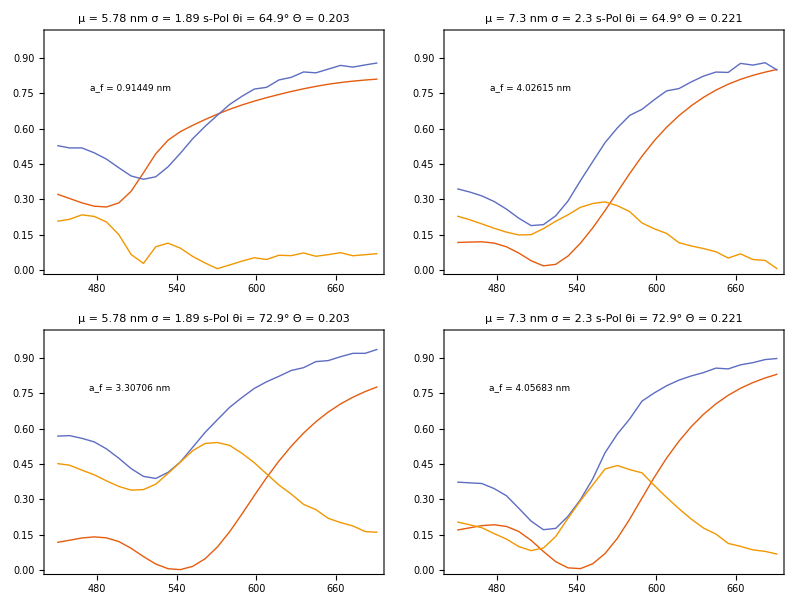

```mathematica
indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
algo3 = Array[(a = radsPol[[#1,#2]];
            cf = Abs@cfracsPol[[#1,#2]];
            b = offsPol[[#1,#2]];
            sigma = muSigma[[#2,2]];
            f = b*norm2[CSMBioReflectionInt[ang[[#1]],indAu,lambda,cf,{a,sigma},"SizeDistribution"->"Normal"][[pol]]])&,
Dimensions[radsPol]];(*pol, ang,case*)

lb = Array[(sigma = "μ = "<>ToString@muSigma[[#2,1]]<>" nm σ = "<>ToString@muSigma[[#2,2]];
       pol = {"s-Pol","p-Pol"}[[1]];
       cf = "Θ = "<>ToString@cfrac[[#2]];
       deg = "θi = "<> ToString[ang[[#1]]/Degree]<>"°";
        sigma<>" "<>pol<>" "<>deg<>" "<>cf)&,
{2,2}];

Grid@MapThread[ListLinePlot[{#1,#2[[take,2]],Abs[#1-#2[[take,2]]]},DataRange->lambda[[{1,-1}]],PlotRange->1,PlotLabel->Style[#3,texStyle],Evaluate[graphsOptsExp],
Epilog->{Inset[Style["a_f = "<> ToString@#4<>" nm",texStyle],{505,.775}](*,
Inset[Style["b = "<> ToString@#5,texStyle],{505,.6}]*)}]&,{algo3,spectra[[pol]],lb,radsPol,ampsPol},2]
```

### FitModel (Gradient Descend) s Pol - Radius add

```mathematica
spectra//Dimensions (*[[pol, ang, thickness, lda, Ext]]*)
wl = spectra[[1,1,1,;;,1]];
take = Range[1,1569,36];
lambda = wl[[take]];

Map[ListPlot[{#[[take,2]],#[[take,2]]},DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsExp]]&,spectra[[1]],{2}]
```

{2,2,2,1569,2}

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
pol = 1; (*s Pol*)
bestRadius = ParallelTable[sigma = muSigma[[c,2]];
            f = norm2[CSMBioReflectionInt[ang[[t]],indAu,lambda,cfrac[[c]],{#,sigma},"SizeDistribution"->"Normal"][[pol]]]&;
            y = spectra[[pol,t,c,take,2]];
            error = Plus @@ (#2 + f[#1] - y)^2/Length[lambda]&;
            result = AbsoluteTiming[
            Prepend[NGradientDescent[error,{5.,.5},LearningRate -> "Barzilai-Borwein",Tolerance-> 1.*^-8],
            {{"s Pol","p Pol"}[[pol]], ang[[t]]*180./Pi,muSigma[[c,1]]}]];
            Print[{Date[], "\n", result}];
            result[[2]],
      {t, Length[ang]},
      {c,Length[muSigma]}];
      
exportData = Prepend[Flatten[Array[Flatten[bestRadius[[#1,#2]]] &,{2,2}],1],
{"Pol", "ang","mu","Best Radius","add","Error"}];
TableForm[exportData]
Export["0-BestRadiusAddFit-SPol-450nm-900nm.csv",exportData];
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{2023,3,23,5,56,59.568887},
,{2515.98,{{s Pol,72.9,5.78},{3.37414,-0.186751},4.4×10^-7}}}

{{2023,3,23,6,2,25.720589},
,{2842.13,{{s Pol,64.9,5.78},{3.37745,-0.208407},4.4×10^-7}}}

{{2023,3,23,6,22,30.097459},
,{1530.53,{{s Pol,72.9,7.3},{4.13756,-0.260155},4.4×10^-7}}}

{{2023,3,23,6,32,19.775534},
,{1794.05,{{s Pol,64.9,7.3},{4.13554,-0.246737},4.4×10^-7}}}

Pol | ang | mu | Best Radius | add | Error
s Pol | 64.9 | 5.78 | 3.37745 | -0.208407 | 4.4×10^-7
s Pol | 64.9 | 7.3 | 4.13554 | -0.246737 | 4.4×10^-7
s Pol | 72.9 | 5.78 | 3.37414 | -0.186751 | 4.4×10^-7
s Pol | 72.9 | 7.3 | 4.13756 | -0.260155 | 4.4×10^-7

```mathematica
sPol = Drop[Import["0-BestRadiusAddFit-SPol-450nm-900nm.csv","Data"],1];
radsPol = Partition[#[[4]]&/@ sPol,2]
ampsPol = Partition[#[[5]]&/@ sPol,2]
```

{{3.37745,4.13554},{3.37414,4.13756}}

{{-0.208407,-0.246737},{-0.186751,-0.260155}}

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

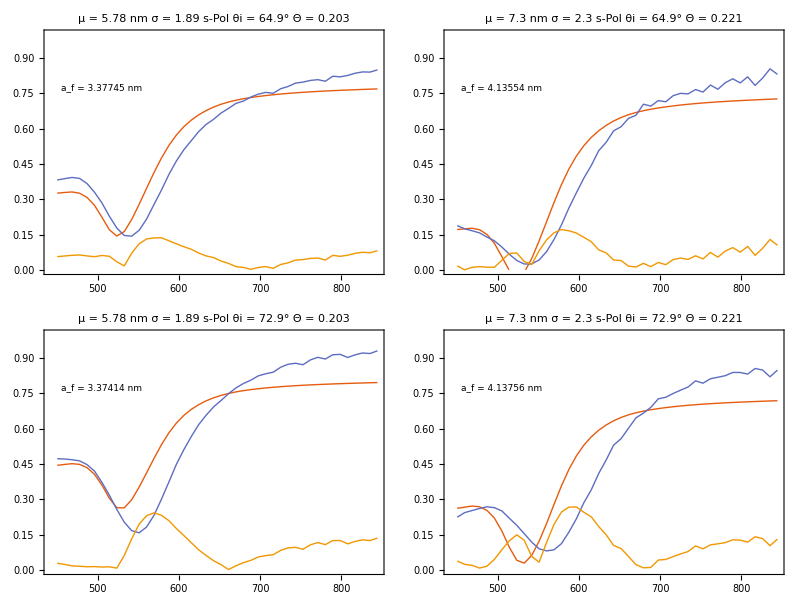

```mathematica
indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
algo3 = Array[(a = radsPol[[#1,#2]];
            b = ampsPol[[#1,#2]];
            sigma = muSigma[[#2,2]];
            f = b+norm2[CSMBioReflectionInt[ang[[#1]],indAu,lambda,cfrac[[#2]],{a,sigma},"SizeDistribution"->"Normal"][[pol]]])&,
Dimensions[radsPol]];(*pol, ang,case*)

lb = Array[(sigma = "μ = "<>ToString@muSigma[[#2,1]]<>" nm σ = "<>ToString@muSigma[[#2,2]];
       polL = {"s-Pol","p-Pol"}[[pol]];
       cf = "Θ = "<>ToString@cfrac[[#2]];
       deg = "θi = "<> ToString[ang[[#1]]/Degree]<>"°";
        sigma<>" "<>polL<>" "<>deg<>" "<>cf)&,
{2,2}];

Grid@MapThread[ListLinePlot[{#1,#2[[take,2]],Abs[#1-#2[[take,2]]]},DataRange->lambda[[{1,-1}]],PlotRange->1,PlotLabel->Style[#3,texStyle],Evaluate[graphsOptsExp],
Epilog->{Inset[Style["a_f = "<> ToString@#4<>" nm",texStyle],{505,.775}](*,
Inset[Style["b = "<> ToString@#5,texStyle],{505,.6}]*)}]&,{algo3,spectra[[pol]],lb,radsPol,ampsPol},2]
```